```mathematica
SetDirectory[NotebookDirectory[]]
```

/Users/yinshi/Documents/work/post-doc-Humboldt/github/Moat-meanfield/MF_DR/spec/gif_data/T50_mu

```mathematica
Re1=Table[Flatten[Import["./Sigma_data_v1/RedataT50mu"<>ToString[i]<>".dat"],0],{i,100,500,5}];
Im1=Table[Flatten[Import["./Sigma_data_v1/ImdataT50mu"<>ToString[i]<>".dat"],0],{i,100,500,5}];
omega=Table[i,{i,1,701,7}]
ps=Table[i,{i,1,501,7}]
Reall=Table[Flatten[Table[{x=omega[[j]],y=ps[[i]],Re1[[k]][[i]][[j]]},{i,1,Length[ps]},{j,1,Length[omega]}],1],{k,1,Length[Re1]}];
Imall=Table[Flatten[Table[{x=omega[[j]],y=ps[[i]],Im1[[k]][[i]][[j]]},{i,1,Length[ps]},{j,1,Length[omega]}],1],{k,1,Length[Re1]}];
spec=Table[Flatten[Table[{x=omega[[j]],y=ps[[i]],-1/π*(Im1[[k]][[i]][[j]]-10)/((Re1[[k]][[i]][[j]])^2+(Im1[[k]][[i]][[j]]-10)^2)},{i,1,Length[ps]},{j,1,Length[omega]}],1],{k,1,Length[Re1]}];
spec2=Table[-1/π*(Im1[[k]]-5)/(Re1[[k]]^2+(Im1[[k]]-5)^2),{k,1,Length[Re1]}];
```

{1,8,15,22,29,36,43,50,57,64,71,78,85,92,99,106,113,120,127,134,141,148,155,162,169,176,183,190,197,204,211,218,225,232,239,246,253,260,267,274,281,288,295,302,309,316,323,330,337,344,351,358,365,372,379,386,393,400,407,414,421,428,435,442,449,456,463,470,477,484,491,498,505,512,519,526,533,540,547,554,561,568,575,582,589,596,603,610,617,624,631,638,645,652,659,666,673,680,687,694,701}

{1,8,15,22,29,36,43,50,57,64,71,78,85,92,99,106,113,120,127,134,141,148,155,162,169,176,183,190,197,204,211,218,225,232,239,246,253,260,267,274,281,288,295,302,309,316,323,330,337,344,351,358,365,372,379,386,393,400,407,414,421,428,435,442,449,456,463,470,477,484,491,498}

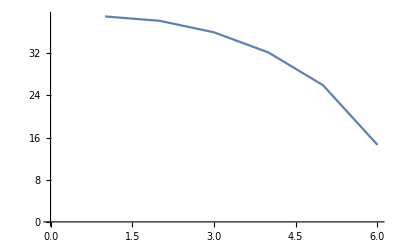

```mathematica
ListLinePlot[√(Re1[[4]][[1]][[1;;10]]-17000)]
```

```mathematica
intRe=Table[Interpolation[Reall[[i]]],{i,1,Length[Re1]}];
intIm=Table[Interpolation[Imall[[i]]],{i,1,Length[Re1]}];
```

```mathematica
CloseKernels[];
LaunchKernels[18];
$KernelCount
```

18

```mathematica
Reintdata=ParallelTable[Table[intRe[[i]][omega1,ps1],{omega1,1,701,2},{ps1,1,498,2}],{i,1,Length[Re1]}];
```

```mathematica
Dimensions[Reintdata]
```

{81,351,249}

```mathematica
Imintdata=ParallelTable[Table[intIm[[i]][omega1,ps1],{omega1,1,701,2},{ps1,1,498,2}],{i,1,Length[Re1]}];
```

```mathematica
Dimensions[Imintdata]
```

{81,351,249}

```mathematica
specint=Table[-1/π*(Imintdata[[k]]-10)/((Reintdata[[k]]-5000)^2+(Imintdata[[k]]-10)^2),{k,1,Length[Re1]}];
```

```mathematica
Table[Export["./spec_data_v1/rhoT50mu"<>ToString[100+(i-1)*5]<>".dat",specint[[i]]],{i,1,Length[Re1]}];
```

```mathematica
ListPlot3D[specint[[1]]]
```

-Graphics3D-